```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[{GraphList[[i]]}][[1]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
GreedyDirectedPartLoop[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* （新）Greedyを使った枝のランクを入力とした有向部分巡回路の構築(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeRulesLine[LineList_]:=Table[i[[1]]-> i[[2]],{i,ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]}](* Edge Rules list from Line list: Lineのリストから枝の規則のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRulesLine[MeshCells[mesh,1]](* Edge Rules list from Mesh: MeshRegionのリストから枝の規則を出力 *)
```

```mathematica
InVertex[PartLoop_]:=DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop],OutVertex[PartLoop]]](* PartLoopの内側の頂点 *)
```

```mathematica
InEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Subsets[InVertex[PartLoop],{2}]]](* PartLoopよりも内側の枝をランク順に出力 *)
```

```mathematica
GreedyRank[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeList[UndirectedGraph[{EdgeRules[Gout][[Rank[[i]]]]}]][[1]];
EdgeAssumption=Append[EdgeProcess,AddEdge];
If[Max[VertexDegree[EdgeAssumption]]≤ 2,
PartLoopAssumption=FindCycle[EdgeAssumption,Infinity,All];
If[PartLoopAssumption=={}||PartLoopAssumption≠{} && Length[VertexList[PartLoopAssumption[[1]]]]== Length[Pin],
EdgeProcess=EdgeAssumption;
If[PartLoopAssumption≠{} ,PartLoopProcess=PartLoopAssumption[[1]]],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
PartLoopProcess
)
(* RankからのGreedy *)
```

### 問題の指定

```mathematica
Pin={{9.02338,1.77427},{7.26643,6.1849},{7.52155,3.6151},{1.40444,9.77536},{5.157,0.213355},{3.53522,3.48728},{8.7097,3.87179},{3.68996,0.581059},{1.78431,1.90046},{0.704839,0.356767}}
(*Point input*)
```

{{9.02338,1.77427},{7.26643,6.1849},{7.52155,3.6151},{1.40444,9.77536},{5.157,0.213355},{3.53522,3.48728},{8.7097,3.87179},{3.68996,0.581059},{1.78431,1.90046},{0.704839,0.356767}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

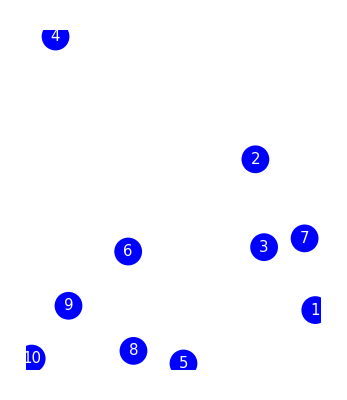

```mathematica
Graphics[{
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

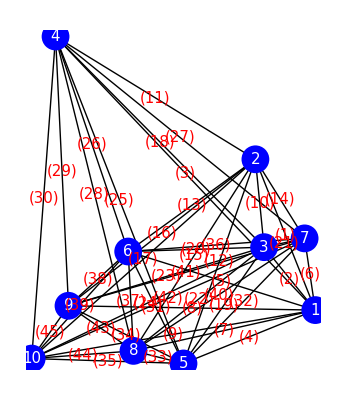

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

### 渦電流の計算

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

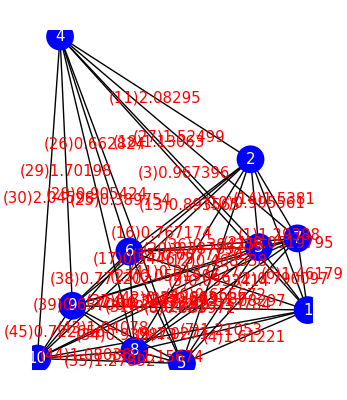

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

### 解の構築

```mathematica
PDRank=Ordering[PD]
```

{21,33,45,6,43,38,2,10,14,37,44,31,34,20,19,4,39,35,13,1,22,32,36,7,5,23,40,12,26,15,11,16,41,8,24,29,9,18,42,17,27,30,28,25,3}

```mathematica
AbsCurr =Abs[Curr ];
```

```mathematica
CurrRank=Ordering[1/AbsCurr ](* 昇順 *)
```

{11,30,29,4,14,27,6,1,35,7,33,18,32,44,43,9,10,3,34,19,28,13,2,38,16,45,26,40,39,8,22,17,37,12,36,25,20,31,42,24,5,23,21,41,15}

```mathematica
PDCurrRank=Ordering[PD/AbsCurr](* 昇順 *)
```

{33,6,14,43,4,10,45,44,2,38,11,35,1,34,19,7,30,29,32,13,37,27,39,18,9,22,16,40,26,20,28,31,3,8,36,12,17,21,25,42,24,5,23,41,15}

```mathematica
PDWeight=PD*Table[1+i*0.1,{i,Length[PD]}][[Ordering[Ordering[PD]]]]
```

{14.2431,4.03876,60.7658,10.8409,20.1225,2.96918,18.5819,31.8567,39.6607,4.64838,28.1841,24.066,13.3523,5.18025,26.5915,29.2225,43.881,41.671,10.3571,9.57211,1.33712,15.1509,21.5567,33.9994,55.4687,25.8932,47.9017,50.2128,36.2667,49.1116,8.03791,16.3187,1.8149,8.67358,12.4725,17.1229,5.82068,3.78077,11.3949,22.2082,30.9621,42.8388,3.47674,6.28642,2.44878}

```mathematica
PDWeightCurrRank=Ordering[PDWeight/AbsCurr ]
```

{33,6,43,14,45,10,38,2,44,4,34,35,37,1,19,11,13,32,7,39,29,30,31,20,21,22,27,40,18,16,9,26,36,12,8,28,3,17,42,24,25,5,23,41,15}

```mathematica
FindShortestTour[Pin]
g1=Graphics[{Line[Pin[[Last[%]]]],Text[Style["Mathematica",FontSize->15],{Center,-0.5}]},PlotRange->{{0,10},{-1,10}}]
```

{32.3545,{1,7,3,2,4,6,9,10,8,5,1}}

-Graphics-

```mathematica
PartLoop1=GreedyRank[PDRank]
DelEdge
EdgeProcess
```

{7<->3,3<->2,2<->6,6<->5,5<->8,8<->9,9<->10,10<->4,4<->1,1<->7}

{1<->3,6<->10,10<->1}

{7<->3,8<->5,9<->10,1<->7,9<->8,3<->2,6<->5,2<->6,4<->10,1<->4}

```mathematica
VertexSortFromLoopEdgeList[PartLoop1]
g2=Graphics[{line=Line[Pin[[%]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],Black,Text[Style["Greedy",FontSize->15],{Center,-0.5}]},PlotRange->{{0,10},{-1,10}}]
ArcLength[line]//N
```

{1,7,3,2,6,5,8,9,10,4,1}

-Graphics-

40.3835

```mathematica
PartLoop2=GreedyRank[CurrRank]
DelEdge
EdgeProcess
```

{2<->4,4<->10,10<->3,3<->6,6<->9,9<->8,8<->5,5<->1,1<->7,7<->2}

{10<->5,10<->8,6<->10}

{2<->4,4<->10,5<->1,7<->2,1<->7,8<->5,9<->8,6<->9,3<->6,10<->3}

{1,7,2,4,10,3,6,9,8,5,1}

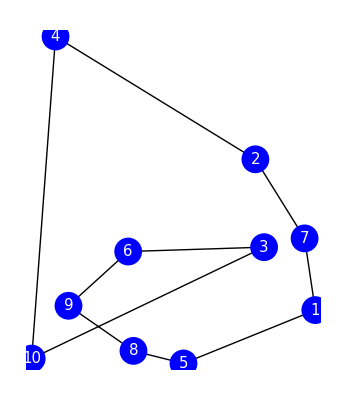

43.0726

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
Graphics[{line=Line[Pin[[%]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
ArcLength[line]//N
```

```mathematica
PartLoop3=GreedyRank[PDCurrRank]
DelEdge
EdgeProcess
```

{8<->5,5<->1,1<->7,7<->2,2<->3,3<->6,6<->4,4<->10,10<->9,9<->8}

{3<->4}

{8<->5,1<->7,7<->2,9<->8,5<->1,3<->2,9<->10,4<->10,4<->6,3<->6}

```mathematica
VertexSortFromLoopEdgeList[PartLoop3]
g3=Graphics[{line=Line[Pin[[%]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],Black,Text[Style["距離÷電流",FontSize->15],{Center,-0.5}]},PlotRange->{{0,10},{-1,10}}]
ArcLength[line]//N
```

{1,7,2,3,6,4,10,9,8,5,1}

-Graphics-

37.3854

```mathematica
PartLoop4=GreedyRank[PDWeightCurrRank]
DelEdge
EdgeProcess
```

{8<->5,5<->1,1<->7,7<->2,2<->3,3<->4,4<->6,6<->10,10<->9,9<->8}

{1<->3,3<->6}

{8<->5,1<->7,9<->8,7<->2,9<->10,3<->2,5<->1,6<->10,3<->4,4<->6}

{1,7,2,3,4,6,10,9,8,5,1}

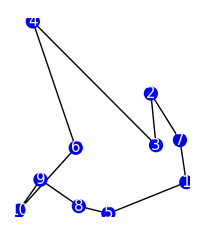

36.8543

```mathematica
VertexSortFromLoopEdgeList[PartLoop4]
Graphics[{line=Line[Pin[[%]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
ArcLength[line]//N
```

### 凸包の内部の点で構成される枝の距離の順位が問題の都市数以内に入る枝の数

```mathematica
ConvexHull=ConvexHullMesh[Pin]
```

-Graphics-

```mathematica
MeshPoint=MeshCoordinates[ConvexHull]
```

{{9.02338,1.77427},{7.26643,6.1849},{1.40444,9.77536},{5.157,0.213355},{8.7097,3.87179},{0.704839,0.356767}}

```mathematica
ConvexHullEdge=EdgeRulesLine[MeshCells[ConvexHull,1]]/. Table[i-> FirstPosition[Pin,MeshPoint[[i]]][[1]],{i,Length[MeshPoint]}]
```

{1→7,7→2,2→4,4→10,10→5,5→1}

```mathematica
InVertexEdge=EdgeNumListVertex[Subsets[InVertex[ConvexHullEdge],{2}]]
```

{20,22,23,37,38,43}

```mathematica
Length[Select[Flatten[Table[FirstPosition[PDRank,InVertexEdge[[i]]],{i,Length[InVertexEdge]}]],#≤10&]]
```

3

```mathematica
Length[Select[Flatten[Table[FirstPosition[PDRank,EdgeNumList[ConvexHullEdge][[i]]],{i,Length[ConvexHullEdge]}]],#≤10&]]
```

2

```mathematica
PDRank
```

{21,33,45,6,43,38,2,10,14,37,44,31,34,20,19,4,39,35,13,1,22,32,36,7,5,23,40,12,26,15,11,16,41,8,24,29,9,18,42,17,27,30,28,25,3}

```mathematica
GraphicsRow[{g1,g2,g3},Epilog->Inset["位置:" ToString[Pin],{Center,0}],ImageSize->1000]
```

-Graphics-

```mathematica
Export["CompGreedy.pdf",GraphicsRow[{g1,g2,g3},Epilog->Inset["位置:" ToString[Pin],{Center,0}],ImageSize->900]]
```

```mathematica
EdgePairDiff[EdgePair1_,EdgePair2_]:=Total[PD[[EdgeNumListVertex[EdgePair1]]]]-Total[PD[[EdgeNumListVertex[EdgePair2]]]]
SelectPair=Select[Subsets[Table[VertexList[{i}],{i,PartLoop1}],{2}],DisjointQ[#[[1]],#[[2]]]&]
CrossNumList=Select[Range[Length[SelectPair]],!RegionDisjoint[Region[Line[Pin[[SelectPair[[#,1]]]]]],Region[Line[Pin[[SelectPair[[#,2]]]]]]]&]
Max[Table[
EdgeVertexPair1={{SelectPair[[i]][[1,1]],SelectPair[[i]][[2,1]]},{SelectPair[[i]][[1,2]],SelectPair[[i]][[2,2]]}};
EdgeVertexPair2={{SelectPair[[i]][[1,1]],SelectPair[[i]][[2,2]]},{SelectPair[[i]][[1,2]],SelectPair[[i]][[2,1]]}};
If[Length[FindCycle[UndirectedGraph[EdgeRules[Gout][[Join[DelEleList[EdgeNumList[EdgeRulesList[PartLoop1]],EdgeNumListVertex[SelectPair[[i]]]],EdgeNumListVertex[EdgeVertexPair1]]]]],Infinity,All]]==1,
EdgePairDiff[SelectPair[[i]],EdgeVertexPair1],EdgePairDiff[SelectPair[[i]],EdgeVertexPair2]]
,{i,CrossNumList}]]
```